```mathematica
Clear["Global`*"]
```

### 関数

```mathematica
LoopMatrix[g_]:=(
FundLoop=FindFundamentalCycles[UndirectedGraph[g]];
RuleFundLoop=Table[EdgeRules[FundLoop[[i]]],{i,Length[FundLoop]}];
RuleRevFundLoop=Table[
EdgeRules[ReverseGraph[Graph[RuleFundLoop[[i]]]]],
{i,Length[FundLoop]}
];
Ruleg=EdgeRules[g];
Table[
Table[
If[MemberQ[RuleFundLoop[[j]],Ruleg[[i]]],1,0]+If[MemberQ[RuleRevFundLoop[[j]],Ruleg[[i]]],-1,0],
{i,EdgeCount[g]}
],
{j,Length[FundLoop]}]
)
```

```mathematica
VertexSortFromLoopEdgeList[LoopEdgeList_]:=(
UndirectedLoop=FindCycle[UndirectedGraph[LoopEdgeList]][[1]];
MinVertexNum=Min[VertexList[UndirectedLoop]];
VertexLoop={MinVertexNum};
For[j=1,Length[VertexLoop]≠ Length[UndirectedLoop],j++,
VertexLoop=Append[VertexLoop,UndirectedLoop[[FirstPosition[UndirectedLoop,VertexLoop[[j]]<->_][[1]],2]]]
];
VertexLoop=Append[VertexLoop,MinVertexNum]
)(* Vertex Sort From Loop Edge List ルールエッジで表現された巡回路から、頂点で表現された巡回路に直す *)
```

```mathematica
DelEle[list_,element_]:=list/.element->Nothing(* Delete Element *)
```

```mathematica
DelEleList[list_,elementlist_]:=list/.Table[i-> Nothing ,{i,elementlist}](* Delete Element *)
```

```mathematica
DelEdgeVertexList[edgelist_,vertexlist_]:=(
devl={};(* Variable of DelEdgeVertexList *)
Do[devl=Union[Position[edgelist,i].{{1},{0}},devl],{i,vertexlist}];
Delete[edgelist,devl]
)(* Delete Edge list from Vertex List 頂点リストから枝リストを削除（頂点リストにある頂点で構成される枝はすべて枝リストから削除）頂点リストに重複があってもUnionがあるのでOK *)
```

```mathematica
EdgeNum[Edge_]:=(
FirstPosition[EdgeRules[Gin],Edge,
FirstPosition[
EdgeRules[Gin],
EdgeRules[
ReverseGraph[{Edge}]
][[1]]
]
][[1]]
) (* Edge Number *)
```

```mathematica
EdgeNumList[Edge_]:=Table[EdgeNum[Edge[[i]]],{i,Length[Edge]}] (* Edge Number List *)
```

```mathematica
EdgeD[Edge_]:=PD[[EdgeNum[Edge]]](* Edge Distance *)
```

```mathematica
EdgeDList[Edge_]:=PD[[EdgeNumList[Edge]]](* Edge Distance *)
```

```mathematica
ListPosRef[list1_,list2_,element_]:=list1[[FirstPosition[list2,element][[1]]]](* list2でのelementの位置に来る、list1の要素を求める(list1にlist2の位置を反映 List Position Reflection) *)
```

```mathematica
EdgeReconst[Edge1_,Side1_,Edge2_,Side2_]:=VertexList[{Edge1}][[Side1]]->VertexList[{Edge2}][[Side2]](* Edge Reconstraction ２つの枝のそれぞれ片方の頂点を使って枝を再構成する *)
```

```mathematica
RestVertex[PartLoop_]:=Delete[VertexList[Gin],Table[{VertexList[PartLoop][[i]]},{i,Length[VertexList[PartLoop]]}]]
```

```mathematica
TriTourDiff[Edge_,Vertex_]:=(
EdgeD[VertexList[{Edge}][[1]]->Vertex]+EdgeD[VertexList[{Edge}][[2]]->Vertex]-EdgeD[Edge]
)(* Triangle Tour Difference *)
```

```mathematica
TriTourDiffList[PartLoop_,Vertex_]:=Table[TriTourDiff[PartLoop[[i]],Vertex],{i,Length[PartLoop]}]
```

```mathematica
MinTriTourDiffPosition[PartLoop_,Vertex_]:=(
FirstPosition[TriTourDiffList[PartLoop,Vertex],Min[TriTourDiffList[PartLoop,Vertex]]][[1]]
)
```

```mathematica
MinEdgeReconstPair[EdgePair_]:=(
ReconstEdgeD1=EdgeD[EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],1]]+EdgeD[EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],2]];
ReconstEdgeD2=EdgeD[EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],2]]+EdgeD[EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],1]];
If[
ReconstEdgeD1<ReconstEdgeD2,
{ReconstEdgeD1,{EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],1],EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],2]}},
{ReconstEdgeD2,{EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],2],EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],1]}}
]
)(* Minimum Edge Reconstraction Pair 枝ペアを再構成し、枝のコストが小さいほうのコストと枝ペアを出力 *)
```

```mathematica
SquareTourDiff[Edge1_,Edge2_]:=(
MinEdgeReconstPair[{Edge1,Edge2}][[1]]-EdgeD[Edge1]-EdgeD[Edge2]
)(* Square Tour Difference *)
```

```mathematica
SquareTourDiffList[PartLoop1_,PartLoop2_]:=Table[SquareTourDiff[i,j],{i,PartLoop1},{j,PartLoop2}]
```

```mathematica
MinSquareTourDiffEdgePair[PartLoop1_,PartLoop2_]:=(
PairNum=FirstPosition[SquareTourDiffList[PartLoop1,PartLoop2],Min[SquareTourDiffList[PartLoop1,PartLoop2]]];
{PartLoop1[[PairNum[[1]]]],PartLoop2[[PairNum[[2]]]]}
)(* 最小のスクエアツアとなるPartLoopの枝ペア *)
```

```mathematica
JoinPartLoop[PartLoop1_,PartLoop2_]:=Join[DelEleList[Join[PartLoop1,PartLoop2],MinSquareTourDiffEdgePair[PartLoop1,PartLoop2]],MinEdgeReconstPair[MinSquareTourDiffEdgePair[PartLoop1,PartLoop2]][[2]]]
```

```mathematica
RestVertexMinCost[PartLoop_]:=Table[Min[TriTourDiffList[PartLoop,i]],{i,RestVertex[PartLoop]}](* 残りの頂点のそれぞれの追加コストが最小になる位置での追加コストのリスト *)
```

```mathematica
MinRestVertex[PartLoop_]:=RestVertex[PartLoop][[
FirstPosition[RestVertexMinCost[PartLoop],Min[RestVertexMinCost[PartLoop]]][[1]]
]](* 残りの頂点の中でも最小の追加コストとなる頂点 *)
```

```mathematica
LoopDelEdge[PartLoop_]:=PartLoop[[MinTriTourDiffPosition[PartLoop,MinRestVertex[PartLoop]]]](* 頂点を追加するときに削除すべき枝 *)
```

```mathematica
InsertVertexLoop[PartLoop_]:=EdgeRules[EdgeAdd[EdgeDelete[PartLoop,LoopDelEdge[PartLoop]],{VertexList[{LoopDelEdge[PartLoop]}][[1]]-> MinRestVertex[PartLoop],MinRestVertex[PartLoop]-> VertexList[{LoopDelEdge[PartLoop]}][[2]]}]](* １つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
ContinuousInsertVertexLoop[PartLoop_]:=(
PartLoopSolution={PartLoop};
For[j=1,Min[RestVertexMinCost[PartLoopSolution[[-1]]]]≤1,
PartLoopSolution=Append[PartLoopSolution,InsertVertexLoop[PartLoopSolution[[-1]]]]
];
PartLoopSolution)(* 連続で１つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
OutVertex[PartLoop_]:=Table[If[!RegionMember[
Polygon[Pin[[VertexSortFromLoopEdgeList[PartLoop]]]],Pin[[i]]
],i],{i,Range[Length[Pin]]}]/.Null->Nothing(* PartLoopの外側の頂点 *)
```

```mathematica
InsertDetachedEdge[PartLoop_,DetachedEdge_]:=Join[DelEleList[Append[PartLoop,DetachedEdge],{MinSquareTourDiffEdgePair[PartLoop,{DetachedEdge}][[1]]}],MinEdgeReconstPair[MinSquareTourDiffEdgePair[PartLoop,{DetachedEdge}]][[2]]](* PartLoopのどの頂点にも接していない枝を挿入 *)
```

```mathematica
EdgeLoopSide[PartLoop_,ContactEdge_]:=Intersection[VertexList[PartLoop],VertexList[{ContactEdge}]][[1]](* PartLoopに接する枝のPartLoop側の頂点 *)
```

```mathematica
EdgeRestSide[PartLoop_,ContactEdge_]:=DelEle[VertexList[{ContactEdge}],EdgeLoopSide[PartLoop,ContactEdge]][[1]](* PartLoopに接する枝のPartLoop側でない頂点 *)
```

```mathematica
DelEdgeContactEdge[PartLoop_,ContactEdge_]:=PartLoop[[MinTriTourDiffPosition[PartLoop,EdgeRestSide[PartLoop,ContactEdge]]]](* PartLoopに接する枝を挿入する際に削除すべき枝 *)
```

```mathematica
InsertContactEdge[PartLoop_,ContactEdge_]:=Join[DelEle[PartLoop,DelEdgeContactEdge[PartLoop,ContactEdge]],{ContactEdge,EdgeRestSide[PartLoop,ContactEdge]->DelEle[VertexList[{DelEdgeContactEdge[PartLoop,ContactEdge]}],EdgeLoopSide[PartLoop,ContactEdge]][[1]]}](* PartLoopの頂点に接する枝を挿入 *)
```

```mathematica
InsertEdge[PartLoop_,ContactEdge_]:=If[IntersectingQ[VertexList[PartLoop],VertexList[{ContactEdge}]],InsertContactEdge[PartLoop,ContactEdge],InsertDetachedEdge[PartLoop,ContactEdge]](* PartLoopの頂点に接する枝か否かを判定し、枝を挿入 *)
```

```mathematica
EdgeNumListVertex[VertexPairList_]:=EdgeNumList[Table[i[[1]]-> i[[2]],{i,VertexPairList}]](* Edge Num List from Vertex 枝の頂点ペアのリストから枝番号のリストを出力 *)
```

```mathematica
ComplementIntersection[List1_,List2_]:=Complement[List1∪List2,List1∩List2](* 2つのリストの共通集合の補集合を求める *)
```

```mathematica
EdgeRulesList[GraphList_]:=Table[EdgeRules[{GraphList[[i]]}][[1]],{i,Length[GraphList]}](* <->や->で表現されるグラフリストを枝の規則のリスト群に変換する *)
```

```mathematica
GreedyDirectedPartLoop[Rank_]:=(
DelEdge={};
EdgeProcess={};
PartLoopProcess={};
For[i=1,PartLoopProcess=={},i++,
AddEdge=EdgeRules[Gout][[Rank[[i]]]];
If[(PartLoopProcess=FindCycle[Graph[Append[EdgeProcess,AddEdge]],Infinity,All])=={},
If[FindCycle[UndirectedGraph[Append[EdgeProcess,AddEdge]],Infinity,All]=={},
EdgeProcess=Append[EdgeProcess,AddEdge],
DelEdge=Append[DelEdge,AddEdge];
]
]
];
EdgeRulesList[PartLoopProcess][[1]]
)
(* （新）Greedyを使った枝のランクを入力とした有向部分巡回路の構築(有向閉路ではないが無向閉路となるとき枝を加えない) *)
```

```mathematica
InsertVertex[PartLoop_,Vertex_]:=(
DelEdgeNum=MinTriTourDiffPosition[PartLoop,Vertex];
Join[Delete[PartLoop,DelEdgeNum],EdgeRules[Gout][[EdgeNumListVertex[{{PartLoop[[DelEdgeNum,1]],Vertex},{PartLoop[[DelEdgeNum,2]],Vertex}}]]]]
)(* 挿入したい１つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
SortSameAs[ReferredList_,SortedList_]:=DelEleList[ReferredList,DelEleList[ReferredList,SortedList]](* 参照するリストと同じ並びでリストを並べ替える(参照するリストにない要素がある場合、その要素は出力されない) *)
```

```mathematica
OutEdgeRank[PartLoop_,Rank_]:=SortSameAs[Rank,EdgeNumListVertex[Join[Subsets[OutVertex[PartLoop],{2}],Tuples[{OutVertex[PartLoop],VertexList[PartLoop]}]]]](* PartLoopの頂点を使う枝を含む、PartLoopよりも外側の枝をランク順に出力 *)
```

```mathematica
EdgeRulesLine[LineList_]:=Table[i[[1]]-> i[[2]],{i,ToExpression[StringDelete[ToString[LineList],{"Line[","]"}]]}](* Edge Rules list from Line list: Lineのリストから枝の規則のリストを出力 *)
```

```mathematica
EdgeRulesMesh[mesh_]:=EdgeRulesLine[MeshCells[mesh,1]](* Edge Rules list from Mesh: MeshRegionのリストから枝の規則を出力 *)
```

```mathematica
InVertex[PartLoop_]:=DelEleList[Range[Length[Pin]],Join[VertexList[PartLoop],OutVertex[PartLoop]]](* PartLoopの内側の頂点 *)
```

```mathematica
InEdgeRank[PartLoop_,Rank_]:=SortSameAs[Rank,EdgeNumListVertex[Subsets[InVertex[PartLoop],{2}]]](* PartLoopよりも内側の枝をランク順に出力 *)
```

```mathematica
GreedyRank[Rank_]:=(
DelEdge={};
EdgeProcess={};
PartLoopProcess={};
For[i=1,PartLoopProcess=={},i++,
AddEdge=EdgeList[UndirectedGraph[{EdgeRules[Gout][[Rank[[i]]]]}]][[1]];
EdgeAssumption=Append[EdgeProcess,AddEdge];
If[Max[VertexDegree[EdgeAssumption]]≤ 2,
PartLoopAssumption=FindCycle[EdgeAssumption,Infinity,All];
If[PartLoopAssumption=={}||PartLoopAssumption≠{} && Length[VertexList[PartLoopAssumption[[1]]]]== Length[Pin],
EdgeProcess=EdgeAssumption;
If[PartLoopAssumption≠{} ,PartLoopProcess=PartLoopAssumption[[1]]],
DelEdge=Append[DelEdge,AddEdge];
]
]
];
PartLoopProcess
)
(* RankからのGreedy *)
```

### 問題の指定

```mathematica
Pin={{9.25288,8.29378},{2.70712,8.11709},{9.07998,1.31631},{1.93951,5.50628},{7.72967,0.273102},{8.12179,9.14533},{7.65083,7.41157},{1.62292,8.16103},{9.49436,8.82514},{1.10565,8.81871}}
(*Point input*)
```

{{9.25288,8.29378},{2.70712,8.11709},{9.07998,1.31631},{1.93951,5.50628},{7.72967,0.273102},{8.12179,9.14533},{7.65083,7.41157},{1.62292,8.16103},{9.49436,8.82514},{1.10565,8.81871}}

```mathematica
Gin=DirectedGraph[CompleteGraph[Length[Pin],VertexLabels->"Name",EdgeLabels->"Name"],"Acyclic"];
```

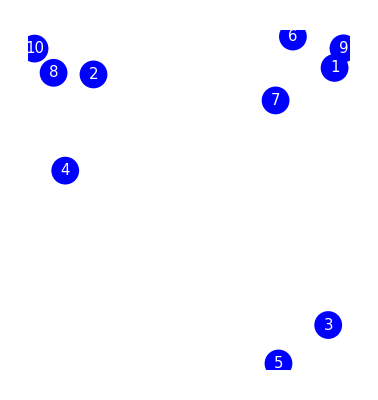

```mathematica
Graphics[{
Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```

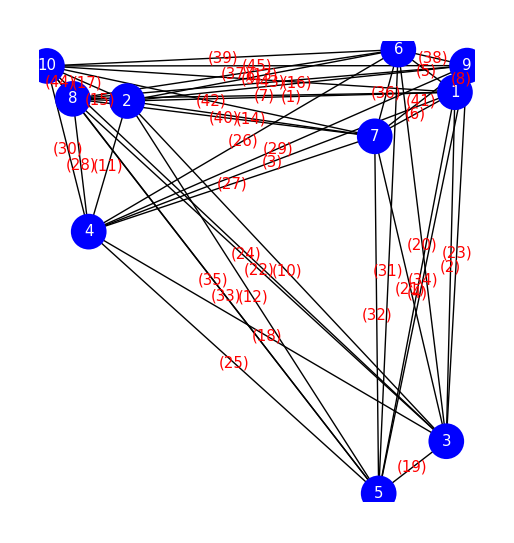

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gin]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[Style["("<>TextString[i]<>")",FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```

### 渦電流の計算

```mathematica
h=LoopMatrix[Gin];
PD=Table[
EuclideanDistance[
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[1,1]]]],
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[2,1]]]]
],
{i,Length[EdgeRules[Gin]]}];(* Point Distance *)
r=IdentityMatrix[Length[EdgeRules[Gin]]]PD;
s=Table[0,{i,Length[EdgeRules[Gin]]}];
FLP=Table[
Pin[[
ConnectedComponents[RuleFundLoop[[i]]][[1]]
]],
{i,Length[RuleFundLoop]}];(* Fundamental Loop Point *)
LoopSpin=Table[
If[(Append[FLP[[i,2]]-FLP[[i,1]],0]×Append[FLP[[i,3]]-FLP[[i,2]],0]).{0,0,1}>0,1,-1],
{i,Length[RuleFundLoop]}];(* 右回りならば負、左回りならば正 *)
FLA=Table[
Area[Polygon[
Pin[[ConnectedComponents[RuleFundLoop[[i]]][[1]]]]
]],
{i,Length[RuleFundLoop]}];(* Fundamental Loop Area *)
U=Table[LoopSpin[[i]]FLA[[i]],{i,Length[RuleFundLoop]}];(* 誘導起電力は右回りなら負、左回りなら正 *)
Curr=Transpose[h].Inverse[h.r.Transpose[h]].(h.s+U);(* 誘導起電力行列を考慮した電流を求める式 *)
```

```mathematica
Gout=Graph[Table[If[Curr[[i]]>0,
VertexList[{EdgeRules[Gin][[i]]}][[1]]->VertexList[{EdgeRules[Gin][[i]]}][[2]],
VertexList[{EdgeRules[Gin][[i]]}][[2]]->VertexList[{EdgeRules[Gin][[i]]}][[1]]
],{i,Length[EdgeRules[Gin]]}
]];(* 電流値の正負をグラフの向きに反映した出力グラフ *)
```

### TSPの解

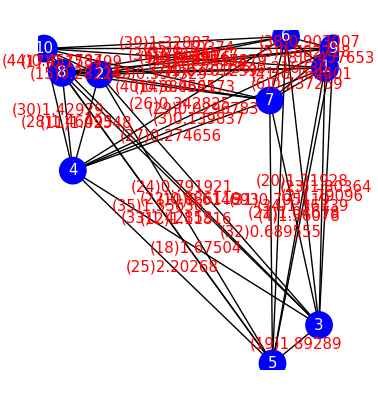

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gout][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gout][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gout]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[Style["("<>TextString[i]<>")"<>TextString[Abs[Curr[[i]]]],FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```

### 解の構築

```mathematica
PDRank=Ordering[PD]
```

{8,44,15,38,5,19,17,36,6,41,28,11,30,14,13,27,40,21,1,37,42,16,2,39,32,26,23,7,25,3,20,43,4,9,29,18,45,34,31,12,10,33,22,35,24}

```mathematica
AbsCurr =Abs[Curr ];
```

```mathematica
CurrRank=Ordering[1/AbsCurr ](* 昇順 *)
```

{25,19,23,2,18,28,30,33,34,4,35,39,20,13,12,37,45,21,11,38,9,22,16,43,5,31,24,1,32,7,10,42,44,8,14,40,26,15,27,6,36,41,17,3,29}

```mathematica
PDCurrRank=Ordering[PD/AbsCurr](* 昇順 *)
```

{19,8,38,5,28,44,30,11,25,15,2,23,13,18,39,37,21,4,34,20,33,45,16,6,35,36,12,43,9,1,32,14,31,7,17,22,42,24,41,10,40,26,27,3,29}

```mathematica
PDWeight=PD*Table[1+i*0.1,{i,Length[PD]}][[Ordering[Ordering[PD]]]]
```

{18.9896,23.0327,31.3064,35.1053,2.12371,3.4749,28.9982,0.642023,35.9221,47.5324,5.98689,46.571,13.7786,11.9851,1.41062,21.837,2.97232,38.0835,2.73016,32.3385,17.5296,53.6474,27.8249,60.2183,30.438,25.8256,15.6539,5.61448,37.1327,7.85628,43.5164,24.9862,51.8729,41.9146,58.3862,3.23386,19.719,1.97319,23.8807,16.4007,4.6462,20.7537,33.1775,1.00407,39.4269}

```mathematica
PDWeightCurrRank=Ordering[PDWeight/AbsCurr ]
```

{8,19,38,44,5,28,15,30,11,13,2,25,6,36,23,21,37,39,17,18,16,4,14,20,1,41,34,45,32,33,42,43,9,12,35,7,40,31,27,22,26,24,10,3,29}

```mathematica
Ans=FindShortestTour[Pin]
g1=Graphics[{Line[Pin[[Last[%]]]],Text[Style["Mathematica",FontSize->15],{Center,-0.5}]},PlotRange->{{0,10},{-1,10}}]
```

{30.3637,{1,9,6,2,10,8,4,5,3,7,1}}

-Graphics-

```mathematica
PartLoop1=GreedyRank[PDRank]
DelEdge
EdgeProcess
```

{1<->9,9<->6,6<->7,7<->4,4<->2,2<->8,8<->10,10<->5,5<->3,3<->1}

{1<->6,2<->10,7<->1,10<->4}

{1<->9,10<->8,2<->8,9<->6,5<->3,7<->6,2<->4,4<->7,3<->1,10<->5}

```mathematica
VertexSortFromLoopEdgeList[PartLoop1]
line=Line[Pin[[%]]]
PDRankL=ArcLength[line]
PDRankPer=100(PDRankL-Ans[[1]])/Ans[[1]]
g2=Graphics[{line,Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],Black,Text[Style[Round[PDRankPer,0.1]"%  Greedy" ,FontSize->15],{Center,-0.5}]},PlotRange->{{-1,10},{-1,10}}]
```

{1,9,6,7,4,2,8,10,5,3,1}

Line[{{9.25288,8.29378},{9.49436,8.82514},{8.12179,9.14533},{7.65083,7.41157},{1.93951,5.50628},{2.70712,8.11709},{1.62292,8.16103},{1.10565,8.81871},{7.72967,0.273102},{9.07998,1.31631},{9.25288,8.29378}}]

33.9518

11.8171

-Graphics-

```mathematica
PD
```

{6.54814,6.97961,7.82659,8.16403,1.4158,1.8289,7.63111,0.583657,8.16412,9.32008,2.72131,9.31419,5.51144,4.9938,1.08509,6.82407,1.74842,8.27902,1.70635,7.88744,6.26056,10.1222,7.52026,10.9488,7.80462,7.17379,6.02074,2.67356,8.2517,3.41577,8.88089,7.1389,9.97556,8.73221,10.8123,1.79659,6.57299,1.40942,7.02374,6.07432,2.3231,6.69473,7.89941,0.836726,8.38871}

```mathematica
PartLoop2=GreedyRank[CurrRank]
DelEdge
EdgeProcess
```

{4<->5,5<->3,3<->9,9<->10,10<->6,6<->2,2<->1,1<->7,7<->8,8<->4}

{1<->8}

{4<->5,5<->3,3<->9,8<->4,6<->10,6<->2,9<->10,1<->2,7<->8,7<->1}

{1,7,8,4,5,3,9,10,6,2,1}

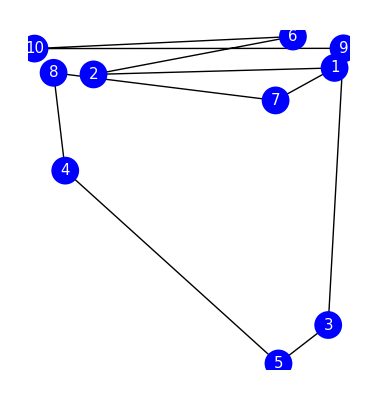

55.08

```mathematica
VertexSortFromLoopEdgeList[PartLoop2]
Graphics[{line=Line[Pin[[%]]],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]
ArcLength[line]//N
```

```mathematica
PartLoop3=GreedyRank[PDCurrRank]
DelEdge
EdgeProcess
```

{5<->3,3<->1,1<->9,9<->6,6<->2,2<->4,4<->8,8<->10,10<->7,7<->5}

{1<->6,10<->4,10<->5}

{5<->3,1<->9,9<->6,8<->4,10<->8,2<->4,3<->1,6<->2,5<->7,7<->10}

```mathematica
VertexSortFromLoopEdgeList[PartLoop3]
line=Line[Pin[[%]]]
PDCurrRankL=ArcLength[line]
PDCurrRankPer=100(PDCurrRankL-Ans[[1]])/Ans[[1]]
g3=Graphics[{line,Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],Black,Text[Style[Round[PDCurrRankPer,0.1]"%  距離÷電流",FontSize->15],{Center,-0.5}]},PlotRange->{{0,10},{-1,10}}]
```

{1,9,6,2,4,8,10,7,5,3,1}

Line[{{9.25288,8.29378},{9.49436,8.82514},{8.12179,9.14533},{2.70712,8.11709},{1.93951,5.50628},{1.62292,8.16103},{1.10565,8.81871},{7.65083,7.41157},{7.72967,0.273102},{9.07998,1.31631},{9.25288,8.29378}}]

36.2557

19.405

-Graphics-

```mathematica
PartLoop4=GreedyRank[PDWeightCurrRank]
DelEdge
EdgeProcess
```

{1<->9,9<->6,6<->2,2<->4,4<->8,8<->10,10<->7,7<->5,5<->3,3<->1}

{1<->6,10<->4}

{1<->9,5<->3,9<->6,10<->8,8<->4,2<->4,6<->2,3<->1,5<->7,7<->10}

{1,9,6,2,4,8,10,7,5,3,1}

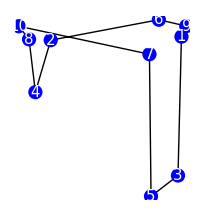

36.2557

```mathematica
VertexSortFromLoopEdgeList[PartLoop4]
Graphics[{line=Line[Pin[[%]]],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]
ArcLength[line]//N
```

```mathematica
GraphicsRow[{g1,g2,g3},Epilog->Inset["位置:" ToString[Pin],{Center,0}],ImageSize->1000]
```

-Graphics-

```mathematica
(*Export["CompGreedy2.pdf",GraphicsRow[{g1,g2,g3},Epilog->Inset[k"番 位置:" ToString[Pin],{Center,0}],ImageSize->900]]*)
```

### クロスの計算

```mathematica
EdgePairDiff[EdgePair1_,EdgePair2_]:=Total[PD[[EdgeNumListVertex[EdgePair1]]]]-Total[PD[[EdgeNumListVertex[EdgePair2]]]]
```

```mathematica
SelectPair=Select[Subsets[Table[VertexList[{i}],{i,PartLoop1}],{2}],DisjointQ[#[[1]],#[[2]]]&]
CrossNumList=Select[Range[Length[SelectPair]],!RegionDisjoint[Region[Line[Pin[[SelectPair[[#,1]]]]]],Region[Line[Pin[[SelectPair[[#,2]]]]]]]&]
Length[CrossNumList] (* クロスの数 *)
```

{{{1,9},{6,7}},{{1,9},{7,4}},{{1,9},{4,2}},{{1,9},{2,8}},{{1,9},{8,10}},{{1,9},{10,5}},{{1,9},{5,3}},{{9,6},{7,4}},{{9,6},{4,2}},{{9,6},{2,8}},{{9,6},{8,10}},{{9,6},{10,5}},{{9,6},{5,3}},{{9,6},{3,1}},{{6,7},{4,2}},{{6,7},{2,8}},{{6,7},{8,10}},{{6,7},{10,5}},{{6,7},{5,3}},{{6,7},{3,1}},{{7,4},{2,8}},{{7,4},{8,10}},{{7,4},{10,5}},{{7,4},{5,3}},{{7,4},{3,1}},{{4,2},{8,10}},{{4,2},{10,5}},{{4,2},{5,3}},{{4,2},{3,1}},{{2,8},{10,5}},{{2,8},{5,3}},{{2,8},{3,1}},{{8,10},{5,3}},{{8,10},{3,1}},{{10,5},{3,1}}}

{23,27}

2

```mathematica
CrossCost=Total[Table[
EdgeVertexPair1={{SelectPair[[i]][[1,1]],SelectPair[[i]][[2,1]]},{SelectPair[[i]][[1,2]],SelectPair[[i]][[2,2]]}};
EdgeVertexPair2={{SelectPair[[i]][[1,1]],SelectPair[[i]][[2,2]]},{SelectPair[[i]][[1,2]],SelectPair[[i]][[2,1]]}};
If[Length[FindCycle[UndirectedGraph[EdgeRules[Gout][[Join[DelEleList[EdgeNumList[EdgeRulesList[PartLoop1]],EdgeNumListVertex[SelectPair[[i]]]],EdgeNumListVertex[EdgeVertexPair1]]]]],Infinity,All]]==1,
EdgePairDiff[SelectPair[[i]],EdgeVertexPair1],EdgePairDiff[SelectPair[[i]],EdgeVertexPair2]]
,{i,CrossNumList}]] (* クロスコスト *)
```

3.13727

```mathematica
RelativeCrossCost=CrossCost/PDRankL (* 相対クロスコスト *)
```

0.0924036